### Setup

```mathematica
SetDirectory[NotebookDirectory[]]
cList={0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.5,0.6,0.7,0.9,1.1};(*tetracycline concentrations*)
sList={0.20951355760625542,0.17161777717267027,0.13372199673908508,0.09582621630549992,0.057930435871914744,0.020034655438329583,-0.004254487243030457,-0.013281192697597165,-0.022307898152163882,-0.0403613090612973,-0.05841471997043071,-0.07646813087956413,-0.11257495269783098,-0.14868177451609782}(*resulting selective differences (see fitness dox.nb)*)
Needs["ErrorBarLogPlots`"](*downloaded from http://library.wolfram.com/infocenter/MathSource/6747/*)
SetOptions[{Plot,BarChart,ListLinePlot,Histogram,SmoothHistogram,ListPlot,ListLinePlot,ListLogLogPlot,ErrorListPlot,ErrorListLogPlot,ListVectorPlot,SmoothDensityHistogram,ErrorListLogLogPlot,ErrorListLogLinearPlot,LogLinearPlot,DistributionChart,LogLogPlot,ParametricPlot,LogPlot,ArrayPlot,DiscretePlot},BaseStyle->{FontColor->Black,PointSize->Large,(*FontFamily->"Arial",*)FontSize->14},AxesStyle->Black,TicksStyle->Black,LabelStyle->{Black,FontSize->14},FrameTicksStyle->Black,Frame->True,FrameStyle->Directive[Thickness[Medium]],PlotRangePadding->{{Scaled[.07],Scaled[.07]},{Scaled[.07],Scaled[.07]}},ImageSize->400,ImagePadding->{{65,65},{65,10}}];
SetOptions[{ListLogPlot,ListLogLogPlot},BaseStyle->{FontColor->Black,PointSize->Large,(*FontFamily->"Arial",*)FontSize->14},AxesStyle->Black,TicksStyle->Black,LabelStyle->{Black,FontSize->14},FrameTicksStyle->Black,Frame->True,FrameStyle->Directive[Thickness[Medium]],PlotRangePadding->{{Scaled[.07],Scaled[.07]},{Scaled[.07],Scaled[.07]}},ImageSize->400,ImagePadding->{{65,65},{65,10}}];
SetOptions[{ListLogLinearPlot},BaseStyle->{FontColor->Black,PointSize->Large,(*FontFamily->"Arial",*)FontSize->14},AxesStyle->Black,TicksStyle->Black,LabelStyle->{Black,FontSize->14},FrameTicksStyle->Black,Frame->True,FrameStyle->Directive[Thickness[Medium]],PlotRangePadding->{{Scaled[.07],Scaled[.07]},{Scaled[.07],None}},ImageSize->400,ImagePadding->{{65,65},{65,10}}];
myticks[min_,max_,n_]:=Table[{i,Switch[Head[i],Integer,i,Rational,N@i,True,i],{0,0.02}},{i,FindDivisions[{min,max},n]}]
myticksfull[lmin_,lmax_,ln_,rmin_,rmax_,rn_]:={{myticks[lmin,lmax,ln],None},{myticks[rmin,rmax,rn],None}}
mycolor[len_List]:=Table[ColorData["DarkRainbow"][(i-1)/(Length@len-1)],{i,1,Length@len}]
mycolor[len_Integer]:=Table[ColorData["DarkRainbow"][(i-1)/(len-1)],{i,1,len}]
```

### Create masks

```mathematica
fns=FileNames["*rough*c2.jpg"];
For[i=1,i≤Length@fns,i++,{
img=Import[fns[[i]]];
Export[NotebookDirectory[]<>"/bin/masks/"<>StringDrop[fns[[i]],-4]<>"_mask.jpg",#]&@(DeleteSmallComponents@DeleteBorderComponents@FillingTransform@Closing[Opening[DeleteSmallComponents@LocalAdaptiveBinarize[Blur@ImageAdjust@GradientFilter[ImageSubtract[img,TopHatTransform[img,2]],11],30],1],1])
}]
```

### Apply masks

```mathematica
fnssmoothMask=FileNames[NotebookDirectory[]<>"/bin/masks/*smooth*c2_mask.jpg"];
fnssmoothMask=SortBy[GatherBy[fnssmoothMask,StringSplit[#,{"="," "}][[11]]&],ToExpression[StringReplace[StringSplit[#[[1]],{"="," "}][[11]],","->"."]]&];
fnssmoothImage=FileNames[NotebookDirectory[]<>"/*smooth*c1.jpg"];
fnssmoothImage=SortBy[GatherBy[fnssmoothImage,StringSplit[#,{"="," "}][[11]]&],ToExpression[StringReplace[StringSplit[#[[1]],{"="," "}][[11]],","->"."]]&];
fnsroughMask=FileNames[NotebookDirectory[]<>"/bin/masks/*rough*c2_mask.jpg"];
fnsroughMask=SortBy[GatherBy[fnsroughMask,StringSplit[#,{"="," "}][[11]]&],ToExpression[StringReplace[StringSplit[#[[1]],{"="," "}][[11]],","->"."]]&];
fnsroughImage=FileNames[NotebookDirectory[]<>"/*rough*c1.jpg"];
fnsroughImage=SortBy[GatherBy[fnsroughImage,StringSplit[#,{"="," "}][[11]]&],ToExpression[StringReplace[StringSplit[#[[1]],{"="," "}][[11]],","->"."]]&];
```

```mathematica
Monitor[For[i=1,i≤Length@fnssmoothImage,i++,{
For[j=1,j≤Length@fnssmoothImage[[i]],j++,{
masked=ImageMultiply[Import[fnssmoothImage[[i,j]]],Binarize[Import[fnssmoothMask[[i,j]]],0.95]],
Export[NotebookDirectory[]<>"/bin/masked/"<>StringSplit[StringDrop[fnssmoothImage[[i,j]],-4],"/"][[-1]]<>"_masked.jpg",masked]
}]}],{i,j}]
Monitor[For[i=1,i≤Length@fnsroughImage,i++,{
For[j=1,j≤Length@fnsroughImage[[i]],j++,{
masked=ImageMultiply[Import[fnsroughImage[[i,j]]],Binarize[Import[fnsroughMask[[i,j]]],0.95]],
Export[NotebookDirectory[]<>"/bin/masked/"<>StringSplit[StringDrop[fnsroughImage[[i,j]],-4],"/"][[-1]]<>"_masked.jpg",masked]
}]}],{i,j}]
```

### Import masked images and compute total area of mutants

```mathematica
fnssmoothMasked=FileNames[NotebookDirectory[]<>"/bin/edited/*smooth*c1.jpg"];
fnssmoothMasked=SortBy[GatherBy[fnssmoothMasked,StringSplit[#,{"="," "}][[11]]&],ToExpression[StringReplace[StringSplit[#[[1]],{"="," "}][[11]],","->"."]]&];
fnssmoothMasks=FileNames[NotebookDirectory[]<>"/bin/masks/*smooth*c2_mask.jpg"];
fnssmoothMasks=SortBy[GatherBy[fnssmoothMasks,StringSplit[#,{"="," "}][[11]]&],ToExpression[StringReplace[StringSplit[#[[1]],{"="," "}][[11]],","->"."]]&];
fnsroughMasked=FileNames[NotebookDirectory[]<>"/bin/edited/*rough*c1.jpg"];
fnsroughMasked=SortBy[GatherBy[fnsroughMasked,StringSplit[#,{"="," "}][[11]]&],ToExpression[StringReplace[StringSplit[#[[1]],{"="," "}][[11]],","->"."]]&];
fnsroughMasks=FileNames[NotebookDirectory[]<>"/bin/masks/*rough*c2_mask.jpg"];
fnsroughMasks=SortBy[GatherBy[fnsroughMasks,StringSplit[#,{"="," "}][[11]]&],ToExpression[StringReplace[StringSplit[#[[1]],{"="," "}][[11]],","->"."]]&];
```

```mathematica
areasSmooth=Table[{},Length@fnssmoothMasked];
totalAreasSmooth=areasSmooth;
Monitor[For[i=1,i<=Length@fnssmoothMasked,i++,{
For[j=1,j≤Length@fnssmoothMasked[[i]],j++,{
img=Import[fnssmoothMasked[[i,j]]],
mask=Import[fnssmoothMasks[[i,j]]],
AppendTo[areasSmooth[[i]],ComponentMeasurements[Binarize[Blur@ImageMultiply[img,mask],0.9],"Area"][[All,2]]],
AppendTo[totalAreasSmooth[[i]],ComponentMeasurements[Binarize[Blur@mask,0.9],"Area"][[All,2]]]
}]
}],{i,j}]
areasRough=Table[{},Length@fnsroughMasked];
totalAreasRough=areasRough;
Monitor[For[i=1,i≤Length@fnsroughMasked,i++,{
For[j=1,j≤Length@fnsroughMasked[[i]],j++,{
img=Import[fnsroughMasked[[i,j]]],
mask=Import[fnsroughMasks[[i,j]]],
AppendTo[areasRough[[i]],ComponentMeasurements[Binarize[Blur@ImageMultiply[img,mask],0.9],"Area"][[All,2]]],
AppendTo[totalAreasRough[[i]],Max@ComponentMeasurements[Binarize[Blur@mask,0.9],"Area"][[All,2]]]

}]
}],{i,j}]
```

### Fraction per clone

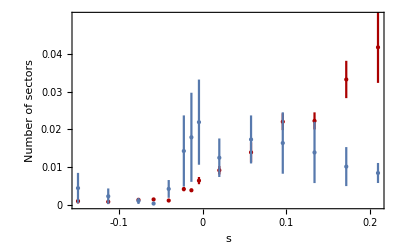

```mathematica
ErrorListPlot[{Transpose[{Transpose[{fDox@cList,Mean/@(Flatten/@areasSmooth)/Mean/@(Flatten/@totalAreasSmooth)}],ErrorBar/@(1/√(Length/@(Flatten/@areasSmooth))StandardDeviation/@(Flatten/@areasSmooth)/Mean/@(Flatten/@totalAreasSmooth))}],Transpose[{Transpose[{fDox@cList,Mean/@(Flatten/@areasRough)/Mean/@(Flatten/@totalAreasRough)}],ErrorBar/@(1/√(Length/@(Flatten/@areasRough))StandardDeviation/@(Flatten/@areasRough)/Mean/@(Flatten/@totalAreasRough))}]},FrameLabel->{"s","Number of sectors"},PlotRange->{Automatic,{0,0.05}},PlotRangePadding->Scaled[.05],PlotStyle->{Darker@Red,Hue[0.6,0.5,0.68]},Frame->{True,True,False,False},FrameTicks->myticksfull[0,0.04,5,-0.2,0.2,5]]
```

### Compute number and size of sectors

```mathematica
sectorsSmooth=Table[{},Length@fnssmoothMasked];
sectorAreasSmooth=sectorsSmooth;
sectorFreqSmooth=sectorsSmooth;
Monitor[For[i=1,i<=Length@fnssmoothMasked,i++,{
For[j=1,j≤Length@fnssmoothMasked[[i]],j++,{
img=Import[fnssmoothMasked[[i,j]]],
mask=Import[fnssmoothMasks[[i,j]]],
areas=Select[Tally@Flatten[MorphologicalComponents@Binarize[img,0.9]ImageData[Dilation[EdgeDetect[Binarize[Blur@mask,0.8]],4]]],#[[1]]≠0&][[All,1]]/.ComponentMeasurements[Binarize[img,0.9],"Area"];
AppendTo[sectorsSmooth[[i]],Length@areas],
AppendTo[sectorAreasSmooth[[i]],areas],
AppendTo[sectorFreqSmooth[[i]],areas/Total@Flatten[ImageData@Binarize[Blur@mask,0.8]]]

}]
}],{i,j}]
sectorsRough=Table[{},Length@fnsroughMasked];
sectorAreasRough=Table[{},Length@fnsroughMasked];
sectorFreqRough=Table[{},Length@fnsroughMasked];
Monitor[For[i=1,i<=Length@fnsroughMasked,i++,{
For[j=1,j≤Length@fnsroughMasked[[i]],j++,{
img=Import[fnsroughMasked[[i,j]]],
mask=Import[fnsroughMasks[[i,j]]],
areas=Select[Tally@Flatten[MorphologicalComponents@Binarize[img,0.9]ImageData[Dilation[EdgeDetect[Binarize[Blur@mask,0.8]],4]]],#[[1]]≠0&][[All,1]]/.ComponentMeasurements[Binarize[img,0.9],"Area"];
AppendTo[sectorsRough[[i]],Length@areas],
AppendTo[sectorAreasRough[[i]],areas],
AppendTo[sectorFreqRough[[i]],areas/Total@Flatten[ImageData@Binarize[Blur@mask,0.8]]]

}]
}],{i,j}]
```

```mathematica
ErrorListLogPlot[{Transpose[{Transpose[{fDox/@cList,Mean/@sectorsSmooth}],ErrorBar[#]&/@(StandardDeviation/@sectorsSmooth/√(Length/@sectorsSmooth))}],Transpose[{Transpose[{fDox/@cList,Mean/@sectorsRough}],ErrorBar[#]&/@(StandardDeviation/@sectorsRough/√(Length/@sectorsRough))}]},FrameLabel->{"s","Number of sectors"},PlotRange->All,PlotRangePadding->Scaled[.05],PlotStyle->{{Darker@Red,PointSize->0.05},{Hue[0.6,0.5,0.68],PointSize->0.05}},AspectRatio->1,ImageSize->300]
Show[ErrorListPlot[{Transpose[{Transpose[{sList,Mean/@(Flatten/@sectorFreqSmooth)}],ErrorBar[#]&/@(StandardDeviation/@sectorFreqSmooth/√(Length/@sectorFreqSmooth))}],Select[Transpose[{Transpose[{sList,Mean/@((Flatten/@sectorFreqRough)/.{}->{0})}],ErrorBar[#]&/@(StandardDeviation/@((Flatten/@sectorFreqRough)/.{}->{0,0})/√(Length/@((Flatten/@sectorFreqRough)/.{}->{0,0})))}],NumberQ@#[[2,1]]&][[1;;7]]},FrameLabel->{"s","Area per sector"},PlotRange->All,PlotRangePadding->Scaled[.05]],
Plot[{A Exp[b y]/.FindFit[Transpose[{sList,Mean/@(Flatten/@sectorFreqSmooth)}],A Exp[b x],{A,b},x],A Exp[b y]/.FindFit[Transpose[{sList,Mean/@((Flatten/@sectorFreqRough)/.{}->{0})}][[1;;7]],A Exp[b x],{A,b},x]},{y,-0.2,0.3}]
]
```

### Compute mutant frequency as a function of radius

```mathematica
freqSmoothR=Table[{},Length@fnssmoothMasked];
Monitor[For[i=1,i≤Length@fnssmoothMasked,i++,{
For[j=1,j≤Length@fnssmoothMasked[[i]],j++,{
img=Binarize[Import[fnssmoothMasked[[i,j]]],0.9],
mask=Binarize[Import[fnssmoothMasks[[i,j]]],0.9],
AppendTo[freqSmoothR[[i]],Select[Quiet@ParallelTable[{Quiet[ComponentMeasurements[Erosion[mask,k],"EquivalentDiskRadius"][[1,2]]],Quiet[(ImageMeasurements[Erosion[mask,k],"TotalIntensity"])^-1 ImageMeasurements[ImageMultiply[img,Erosion[mask,k]],"TotalIntensity"]]},{k,0,ComponentMeasurements[Erosion[mask,0],"EquivalentDiskRadius"][[1,2]],10}],NumberQ@#[[1]]&]]


}]
}],{i,j}]
freqRoughR=Table[{},Length@fnsroughMasked];
Monitor[For[i=1,i≤Length@fnsroughMasked,i++,{
For[j=1,j≤Length@fnsroughMasked[[i]],j++,{
img=Binarize[Import[fnsroughMasked[[i,j]]],0.9],
mask=Binarize[Import[fnsroughMasks[[i,j]]],0.9],
AppendTo[freqRoughR[[i]],Select[Quiet@ParallelTable[{Quiet[ComponentMeasurements[Erosion[mask,k],"EquivalentDiskRadius"][[1,2]]],Quiet[(ImageMeasurements[Erosion[mask,k],"TotalIntensity"])^-1 ImageMeasurements[ImageMultiply[img,Erosion[mask,k]],"TotalIntensity"]]},{k,0,ComponentMeasurements[Erosion[mask,0],"EquivalentDiskRadius"][[1,2]],10}],NumberQ@#[[1]]&]]

}]
}],{i,j}]
```

```mathematica
scale=0.01841620626151013(*mm per pixel*)
```

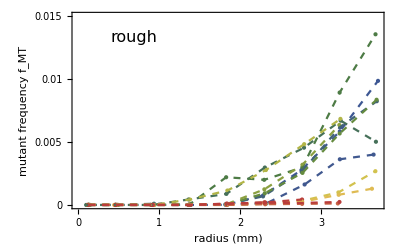

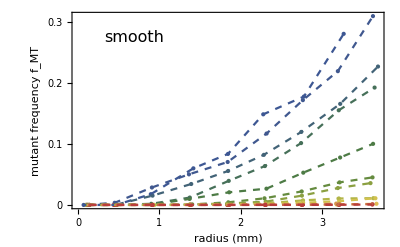

```mathematica
Show[ListPlot[Transpose[{#[[All,1]]scale,#[[All,2]]}]&/@datRough,Epilog->{Text[Style["rough",16],Scaled[{0.2,0.87}]]},FrameLabel->{"radius (mm)","mutant frequency f_MT"},PlotRange->{Automatic,{0,0.015}},PlotStyle->mycolor@Length@freqRoughR,Frame->{True,True,False,False},FrameTicks->myticksfull[0,0.015,5,0,4,5]],ListPlot[Transpose[{#[[All,1]]scale,#[[All,2]]}]&/@datRough,Joined->True,PlotRange->All,PlotStyle->({#,Dashed}&/@(mycolor@Length@freqRoughR))]]
Show[ListPlot[Transpose[{#[[All,1]]scale,#[[All,2]]}]&/@dat,Epilog->{Text[Style["smooth",16],Scaled[{0.2,0.87}]]},FrameLabel->{"radius (mm)","mutant frequency f_MT"},PlotRange->All,PlotStyle->mycolor@Length@freqSmoothR,Frame->{True,True,False,False},FrameTicks->myticksfull[0,0.3,4,0,4,5]],ListPlot[Transpose[{#[[All,1]]scale,#[[All,2]]}]&/@dat,Joined->True,PlotRange->All,PlotStyle->({#,Dashed}&/@(mycolor@Length@freqSmoothR))]]
```

### Linear fits for the sqrt of mutant frequencies

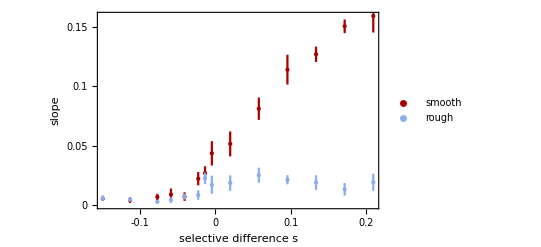

```mathematica
ErrorListPlot[{Transpose[{Transpose[{sList,b/.FindFit[#,b x,{b},x]&/@(Transpose[{scale #[[All,1]],√(#[[All,2]])}]&/@dat)}],ErrorBar@Delete[#/2,0]&@Differences@First@NonlinearModelFit[#,b x,{b},x]["ParameterConfidenceIntervals"]&/@(Transpose[{scale #[[All,1]],√(#[[All,2]])}]&/@dat)}],
Transpose[{Transpose[{sList,b/.FindFit[#,b x,{b},x]&/@(Transpose[{scale #[[All,1]],√(#[[All,2]])}]&/@datRough)}],ErrorBar@Delete[#/2,0]&@Differences@First@NonlinearModelFit[#,b x,{b},x]["ParameterConfidenceIntervals"]&/@(Transpose[{scale #[[All,1]],√(#[[All,2]])}]&/@datRough)}]},PlotStyle->{Darker@Red,ColorData[95][1]},PlotLegends->Placed[{"smooth","rough"},Scaled@{0.2,0.6}],FrameLabel->{"selective difference s","slope"},Frame->{True,True,False,False},FrameTicks->myticksfull[0,scale^-1 0.003,4,-0.2,0.2,5]]
```

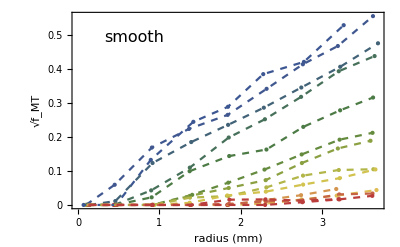

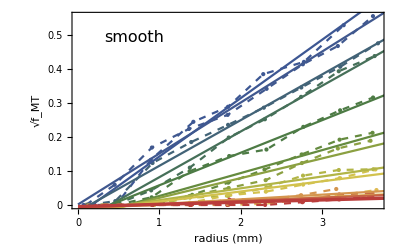

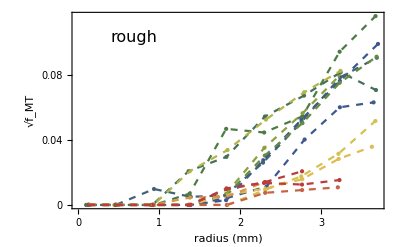

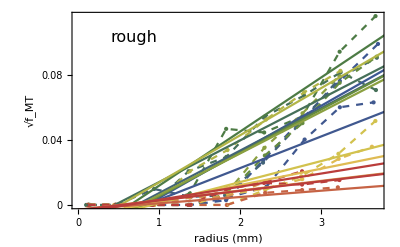

```mathematica
Show[ListPlot[Transpose[{#[[All,1]]scale,√(#[[All,2]])}]&/@dat,Epilog->{Text[Style["smooth",16],Scaled[{0.2,0.87}]]},Frame->{True,True,False,False},FrameTicks->myticksfull[0,0.5,5,0,4,5],FrameLabel->{"radius (mm)","√f_MT"},PlotRange->All,PlotStyle->mycolor@Length@freqSmoothR],ListPlot[Transpose[{#[[All,1]]scale,√(#[[All,2]])}]&/@dat,Joined->True,PlotRange->All,PlotStyle->({#,Dashed}&/@(mycolor@Length@freqSmoothR))]]
Show[ListPlot[Transpose[{#[[All,1]]scale,√(#[[All,2]])}]&/@dat,Epilog->{Text[Style["smooth",16],Scaled[{0.2,0.87}]]},Frame->{True,True,False,False},FrameTicks->myticksfull[0,0.5,5,0,4,5],FrameLabel->{"radius (mm)","√f_MT"},PlotRange->All,PlotStyle->mycolor@Length@freqSmoothR],ListPlot[Transpose[{#[[All,1]]scale,√(#[[All,2]])}]&/@dat,Joined->True,PlotRange->All,PlotStyle->({#,Dashed}&/@(mycolor@Length@freqSmoothR))],Plot[Evaluate[( A+b x1)/.FindFit[#,A+ b x,{A,b},x]&/@(Transpose[{#[[All,1]]scale ,√(#[[All,2]])}]&/@dat)],{x1,0,4},PlotRange->All,PlotStyle->mycolor@freqRoughR]]

Show[ListPlot[Transpose[{#[[All,1]]scale,√(#[[All,2]])}]&/@datRough,Epilog->{Text[Style["rough",16],Scaled[{0.2,0.87}]]},Frame->{True,True,False,False},FrameTicks->myticksfull[0,0.12,6,0,4,5],FrameLabel->{"radius (mm)","√f_MT"},PlotRange->All,PlotStyle->mycolor@Length@freqSmoothR],ListPlot[Transpose[{#[[All,1]]scale,√(#[[All,2]])}]&/@datRough,Joined->True,PlotRange->All,PlotStyle->({#,Dashed}&/@(mycolor@Length@freqSmoothR))]]

Show[ListPlot[Transpose[{#[[All,1]]scale,√(#[[All,2]])}]&/@datRough,Epilog->{Text[Style["rough",16],Scaled[{0.2,0.87}]]},Frame->{True,True,False,False},FrameTicks->myticksfull[0,0.12,6,0,4,5],FrameLabel->{"radius (mm)","√f_MT"},PlotRange->All,PlotStyle->mycolor@Length@freqSmoothR],ListPlot[Transpose[{#[[All,1]]scale,√(#[[All,2]])}]&/@datRough,Joined->True,PlotRange->All,PlotStyle->({#,Dashed}&/@(mycolor@Length@freqSmoothR))],Plot[Evaluate[( A+b x1)/.FindFit[#,A+ b x,{A,b},x]&/@(Transpose[{#[[All,1]]scale ,√(#[[All,2]])}]&/@datRough)],{x1,0,4},PlotRange->All,PlotStyle->mycolor@freqRoughR]]
```

### Plot final mutant frequency

```mathematica
freqSmoothTotal=Table[(Total/@areasSmooth[[i]]/Max/@totalAreasSmooth[[i]]),{i,1,Length@areasSmooth}];
freqRoughTotal=Table[(Total/@areasRough[[i]]/Max/@totalAreasRough[[i]]),{i,1,Length@areasRough}];
```

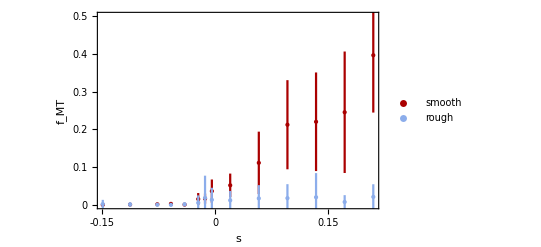

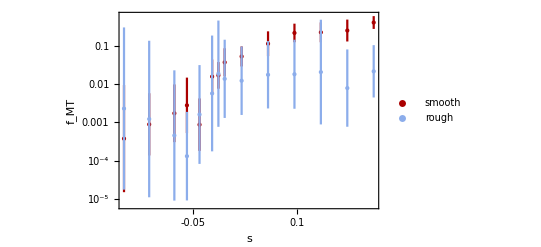

```mathematica
(*SD as error bars*)
Show[ErrorListPlot[{Transpose[{Transpose[{fDox/@cList,Mean/@freqSmoothTotal}],ErrorBar[#]&/@(StandardDeviation/@freqSmoothTotal)}],Transpose[{Transpose[{fDox/@cList,Mean/@freqRoughTotal}],ErrorBar[#]&/@(StandardDeviation/@freqRoughTotal)}]},PlotRangePadding->{{Scaled[.05],Scaled[.05]},{Scaled[.02],Scaled[.13]}},PlotRange->{All,{0,0.5}},FrameLabel->{"s","f_MT"},Frame->{True,True,False,False},FrameTicks->{{myticks[0,0.5,5],None},{myticks[-0.3,0.3,12],None}},PlotStyle->{Darker@Red,ColorData[95][1]},PlotLegends->Placed[{"smooth","rough"},Scaled@{0.2,0.7}]]]
Show[ErrorListLogPlot[{Transpose[{Transpose[{fDox/@cList,Mean/@freqSmoothTotal}],ErrorBar[#]&/@(StandardDeviation/@freqSmoothTotal)}],Transpose[{Transpose[{fDox/@cList,Mean/@freqRoughTotal}],ErrorBar[#]&/@(StandardDeviation/@freqRoughTotal)}]},PlotRangePadding->{{Scaled[.05],Scaled[.05]},{Scaled[.02],Scaled[.13]}},PlotRange->All,PlotStyle->{Darker@Red,ColorData[95][1]},FrameLabel->{"s","f_MT"},Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{myticks[-0.2,0.3,12],None}},PlotLegends->Placed[{"smooth","rough"},Scaled@{0.8,0.15}]]]
```

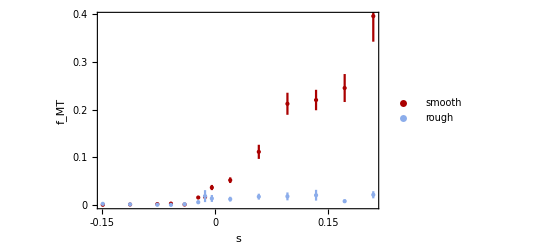

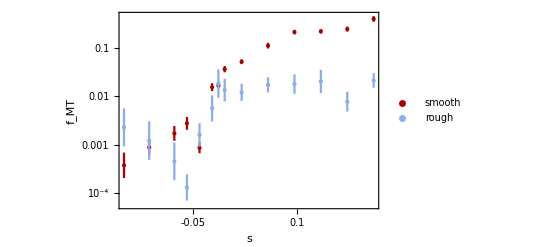

```mathematica
(*SEM as error bars*)
Show[ErrorListPlot[{Transpose[{Transpose[{fDox/@cList,Mean/@freqSmoothTotal}],ErrorBar[#]&/@(StandardDeviation/@freqSmoothTotal/√(Length/@freqSmoothTotal))}],Transpose[{Transpose[{fDox/@cList,Mean/@freqRoughTotal}],ErrorBar[#]&/@(StandardDeviation/@freqRoughTotal/√(Length/@freqRoughTotal))}]},PlotRangePadding->{{Scaled[.05],Scaled[.05]},{Scaled[.02],Scaled[.13]}},PlotRange->All,FrameLabel->{"s","f_MT"},Frame->{True,True,False,False},FrameTicks->{{myticks[0,0.5,5],None},{myticks[-0.3,0.3,12],None}},PlotStyle->{Darker@Red,ColorData[95][1]},PlotLegends->Placed[{"smooth","rough"},Scaled@{0.2,0.7}]]]
Show[ErrorListLogPlot[{Transpose[{Transpose[{fDox/@cList,Mean/@freqSmoothTotal}],ErrorBar[#]&/@(StandardDeviation/@freqSmoothTotal/√(Length/@freqSmoothTotal))}],Transpose[{Transpose[{fDox/@cList,Mean/@freqRoughTotal}],ErrorBar[#]&/@(StandardDeviation/@freqRoughTotal/√(Length/@freqRoughTotal))}]},PlotRangePadding->{{Scaled[.05],Scaled[.05]},{Scaled[.02],Scaled[.13]}},PlotRange->All,PlotStyle->{Darker@Red,ColorData[95][1]},FrameLabel->{"s","f_MT"},Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{myticks[-0.2,0.3,12],None}},PlotLegends->Placed[{"smooth","rough"},Scaled@{0.2,0.7}]]]
```

### Clone size distribution

```mathematica
freqSmooth=Table[Sort/@(areasSmooth[[i]]/Max/@totalAreasSmooth[[i]](*taking max removes tiny component that might get picked up*)),{i,1,Length@areasSmooth}];
freqRough=Table[Sort/@(areasRough[[i]]/Max/@totalAreasRough[[i]]),{i,1,Length@areasRough}];
sfs=Transpose[{#,1-Range@Length@#/Length@#}]&/@(Sort/@(Flatten/@freqSmooth));
sfsRough=Transpose[{#,1-Range@Length@#/Length@#}]&/@(Sort/@(Flatten/@freqRough));
```

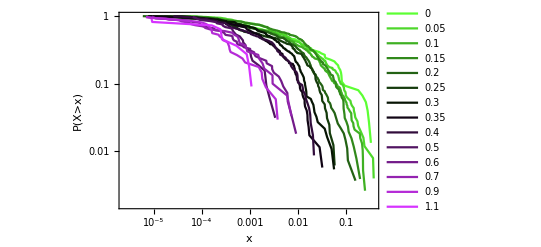

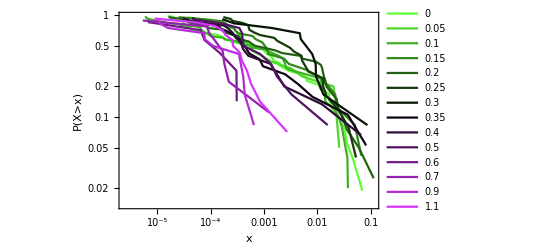

```mathematica
Show[ListLogLogPlot[sfs,Joined->True,PlotStyle->Table[Hue[If[i<8,0.3,0.8],0.8,Abs@(i-7.5)/7/0.93],{i,1,14}],PlotLegends->cList,PlotRange->All,FrameLabel->{"x","P(X>x)"}]]
Show[ListLogLogPlot[sfsRough,Joined->True,PlotStyle->Table[Hue[If[i<8,0.3,0.8],0.8,Abs@(i-7.5)/7/0.93],{i,1,14}],PlotLegends->cList,PlotRange->All,FrameLabel->{"x","P(X>x)"}]]
```